## Twisted Bilayer, Forces along bonds, No Layer Coupling

```mathematica
ClearAll[ex, ey, n, latticepts,unitcellpts,dcutoff,bonds,segmentn,segments,qloop, freqs,D3x3]
```

## Layer Parameters

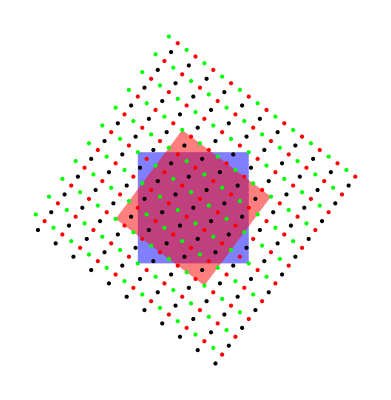

```mathematica
(*Bottom Lattice Vectors*)
ebx={1,0,0};
eby={0,1,0};
(*Moire Twist Parameters*)
lx=3;
ly=4;
lm=√(lx^2+ly^2);
θ=N[ArcTan[ly/lx]];
rot=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
(*Top Lattice Vectors*)
etx=rot.ebx;
ety=rot.eby;
(*Moire Lattice Vectors*)
eMx=(√(lx^2+ly^2))*etx;
eMy=(√(lx^2+ly^2))*ety;
(*Inverse Lattice Vectors*)
Gbx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby)/(ebx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby);
Gby=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx)/(eby.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx);
Gtx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety)/(etx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety);
Gty=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx)/(ety.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx);
GMx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy)/(eMx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy);
GMy=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx)/(eMy.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx);
(*Layer spacing*)
h=1;
(*Graphics*)
bottomBZ=Polygon[1/2{Gbx[[1;;2]]+Gby[[1;;2]],-Gbx[[1;;2]]+Gby[[1;;2]],-Gbx[[1;;2]]-Gby[[1;;2]],Gbx[[1;;2]]-Gby[[1;;2]]}];
topBZ=Polygon[1/2{Gtx[[1;;2]]+Gty[[1;;2]],-Gtx[[1;;2]]+Gty[[1;;2]],-Gtx[[1;;2]]-Gty[[1;;2]],Gtx[[1;;2]]-Gty[[1;;2]]}];
Γpoints=Table[{Black,Point[i*GMx[[1;;2]]+j*GMy[[1;;2]]]},{i,-lm,lm},{j,-lm,lm}];
Xpoints=Table[{Red,Point[(i+.5)*GMx[[1;;2]]+j*GMy[[1;;2]]]},{i,-lm,lm},{j,-lm,lm}];
Mpoints=Table[{Green,Point[(i+.5)*GMx[[1;;2]]+(j+.5)*GMy[[1;;2]]]},{i,-lm,lm},{j,-lm,lm}];
Graphics[{{Opacity[.5],Blue,bottomBZ},{Opacity[.5],Red,topBZ},Γpoints,Xpoints,Mpoints}]
```

## Create Lattice and unit cell

```mathematica
(*Dummy variables for creating unit cell*)
n=50;
δ=.01;
(*Data arrays to store lattice points*)
latticepts={};
unitcellpts={};
(*Loop from -n/2 to n/2 in x and y direction*)
For[i=(-n )/2,i<=n/2,i++,
For[j=(-n)/2,j<=n/2,j++,
(*Add to lattice points for graphics*)
AppendTo[latticepts, i*ebx+j*eby];
AppendTo[latticepts,i*etx+j*ety+{0,0,h}];
(*If lattice point x and y components are within moire unit cell add it to points*)
(*for bottom layer*)
If[-δ<=((i*ebx+j*eby)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*ebx+j*eby)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*ebx+j*eby];
];
(*And top layer*)
If[-δ<=((i*etx+j*ety)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*etx+j*ety)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*etx+j*ety+{0,0,h}];
];
]
]
ListPointPlot3D[unitcellpts,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

## Generate Adjacent Unit Cells

```mathematica
(*This code takes the distance cutoff and determines minimum and maximum x and y values for potential bonds*)
(*It then uses these values to determine which unit cells to increase in the bond-creation loop*)
dcutoff =√2;
(*Bilayer*)
unitcells={};
xmin =Min[unitcellpts.eMx/(√(eMx.eMx))]-dcutoff;
xmax =Max[unitcellpts.eMx/(√(eMx.eMx))]+dcutoff;
ymin=Min[unitcellpts.eMy/(√(eMy.eMy))]-dcutoff;
ymax=Max[unitcellpts.eMy/(√(eMy.eMy))]+dcutoff;
nxmin=Floor[xmin/(√(eMx.eMx))];
nxmax = Ceiling[xmax/(√(eMx.eMx))];
nymin=Floor[ymin/(√(eMy.eMy))];
nymax=Ceiling[ymax/(√(eMy.eMy))];
For[i=nxmin,i<=nxmax,i++,
For[j=nymin,j<=nymax,j++,
AppendTo[unitcells, i*eMx + j*eMy]
];
];
```

## Create List of Bonds Included

```mathematica
(*This code creates bonds*)
(*Bilayer*)
bonds={};
bondgraphics={};

(*Loop over atoms in center unit cell*)
Monitor[For[i=1,i<=Length[unitcellpts],i++,
(*Loop over atoms in other unit cell*)
For[j=1,j<=Length[unitcellpts],j++,
(*Loop over unit cells (from above)*)
For[R=1,R<=Length[unitcells],R++,
(*If distance is within cutoff, and z component is zero*)
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[d*unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<h/2,
(*Create bond*)
(dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Arrow[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];)
];
]
]
],{i,j}];Graphics3D[bilayerbondgraphics]
```

-Graphics3D-

## Create Momentum Loop

```mathematica
segmentn=20;
segments={{0,0,0},1/2 GMx,1/2 GMx+1/2 GMy,{0,0,0}};
qloop={};
For[s=1,s<Length[segments],s++,
For[i=1,i<=segmentn,i++,
AppendTo[qloop,segments[[s]]+i*((segments[[s+1]]-segments[[s]])/segmentn)]
]
]
ListPointPlot3D[qloop]
```

-Graphics3D-

## Main Loop

```mathematica
(*Number of folds, bond strength A, bond decay λ*)
nfolds =6;
A=1;
λ=10;
(*Data arrays*)
freqs={};
(*Loop over momentum space*)
Monitor[For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Bilayer Dynamics Matrix*)
DynamicsMatrix=ConstantArray[0,{3*Length[unitcellpts],3*Length[unitcellpts]}];
(*Bilayer Calculation*)
For[i=1,i<=Length[bonds],i++,
(*Get Bond Information*)
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
(*Compute 3x3 block of dynamics matrix*)
D3x3=A*ⅇ^(-λ*d){{dhat[[1]]^2,dhat[[1]]*dhat[[2]],dhat[[1]]*dhat[[3]]},{dhat[[2]]*dhat[[1]],dhat[[2]]^2,dhat[[2]]*dhat[[3]]},{dhat[[3]]*dhat[[1]], dhat[[3]]*dhat[[2]],dhat[[3]]^2}};
(*Add it to correct blocks of full dynamics matrix*)
DynamicsMatrix[[3a1-2;;3a1,3a1-2;;3a1]]+=-1*D3x3;
DynamicsMatrix[[3a1-2;;3a1,3a2-2;;3a2]]+=D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs,ReverseSort[√(-Eigenvalues[DynamicsMatrix])]];
]
,{k}]
```

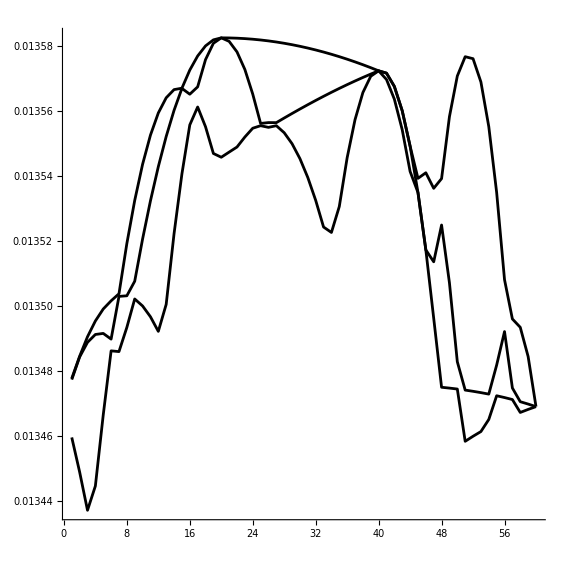

```mathematica
(*Plotting*)
nbands=3;

Show[{ListLinePlot[Table[Re[freqs[[;;,i]]],{i,1,nbands}],PlotStyle->{{Black}}]},
AspectRatio->1,PlotRange->{Min[Table[Re[freqs[[;;,i]]],{i,1,nbands}]],Max[Table[Re[freqs[[;;,i]]],{i,1,nbands}]]}]
```

## Analytic Results

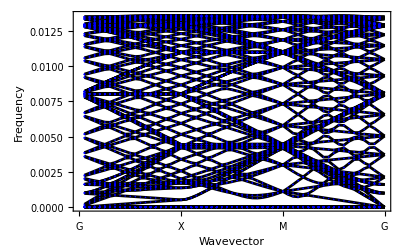

```mathematica
ClearAll[C1,C2,DM]
C1b[q_]:=Sum[ⅇ^(-λ*n)*({{2Cos[n*q.ebx]-2, 0, 0}, {0, 2Cos[n*q.eby]-2, 0}, {0, 0, 0}}),{n,1,dcutoff}]+Sum[If[√(n^2+m^2)<=dcutoff,(ⅇ^(-λ*√(n^2+m^2)))/(n^2+m^2)*({{4 n^2*(Cos[n*q.ebx]Cos[m*q.eby]-1), -4m*n*(Sin[n*q.ebx]*Sin[m*q.eby]), 0}, {-4m*n*(Sin[n*q.ebx]*Sin[m*q.eby]), 4 m^2*(Cos[n*q.ebx]Cos[m*q.eby]-1), 0}, {0, 0, 0}}),0],{n,1,dcutoff},{m,1,dcutoff}]
C1t[q_]:=Sum[ⅇ^(-λ*n)*({{2Cos[n*q.etx]-2, 0, 0}, {0, 2Cos[n*q.ety]-2, 0}, {0, 0, 0}}),{n,1,dcutoff}]+Sum[If[√(n^2+m^2)<=dcutoff,(ⅇ^(-λ*√(n^2+m^2)))/(n^2+m^2)*({{4 n^2*(Cos[n*q.etx]Cos[m*q.ety]-1), -4m*n*(Sin[n*q.etx]*Sin[m*q.ety]), 0}, {-4m*n*(Sin[n*q.etx]*Sin[m*q.ety]), 4 m^2*(Cos[n*q.etx]Cos[m*q.ety]-1), 0}, {0, 0, 0}}),0],{n,1,dcutoff},{m,1,dcutoff}];
DM[q_]:=A*Evaluate[ArrayFlatten[({{C1b[q], 0}, {0, C1t[q]}})]]
analyticfreqs={};
analyticfoldedfreqs={};
nfolds=3;
For[k=1,k<Length[qloop],k++,
AppendTo[analyticfoldedfreqs,{}];
For[a=-nfolds,a<=nfolds,a++,
For[b=-nfolds,b<=nfolds,b++,
q=qloop[[k]]+a*GMx+b*GMy;
analyticfoldedfreqs[[-1]]=ReverseSort[Join[analyticfoldedfreqs[[-1]],√(-Eigenvalues[DM[q]])]];
]
]
]
nbands=150;
Show[ListLinePlot[Table[Abs[freqs[[;;,i]]],{i,1,nbands}],PlotStyle->{{Black}}],ListPlot[Table[Abs[analyticfoldedfreqs[[;;,i]]],{i,1,Length[analyticfoldedfreqs[[1]]]}],PlotStyle->{Blue}],Frame->True,FrameTicks->{{Automatic,None},{{{0,"G"},{segmentn,"X"},{2segmentn,"M"},{3segmentn,"G"}},None}},FrameLabel->{{"Frequency",""},{"Wavevector",""}}]
```